```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/s1220054/Dissertation/Dissertation/DiSamp/src

```mathematica
chidata =Import["chi.txt", "CSV"]
```

{{1,87},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0},{52,0},{53,0},{54,0},{55,0},{56,0},{57,0},{58,0},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0},{67,0},{68,0},{69,0},{70,0},{71,0},{72,0},{73,0},{74,0},{75,0},{76,0},{77,0},{78,0},{79,0},{80,0},{81,0},{82,0},{83,0},{84,0},{85,0},{86,0},{87,0}}

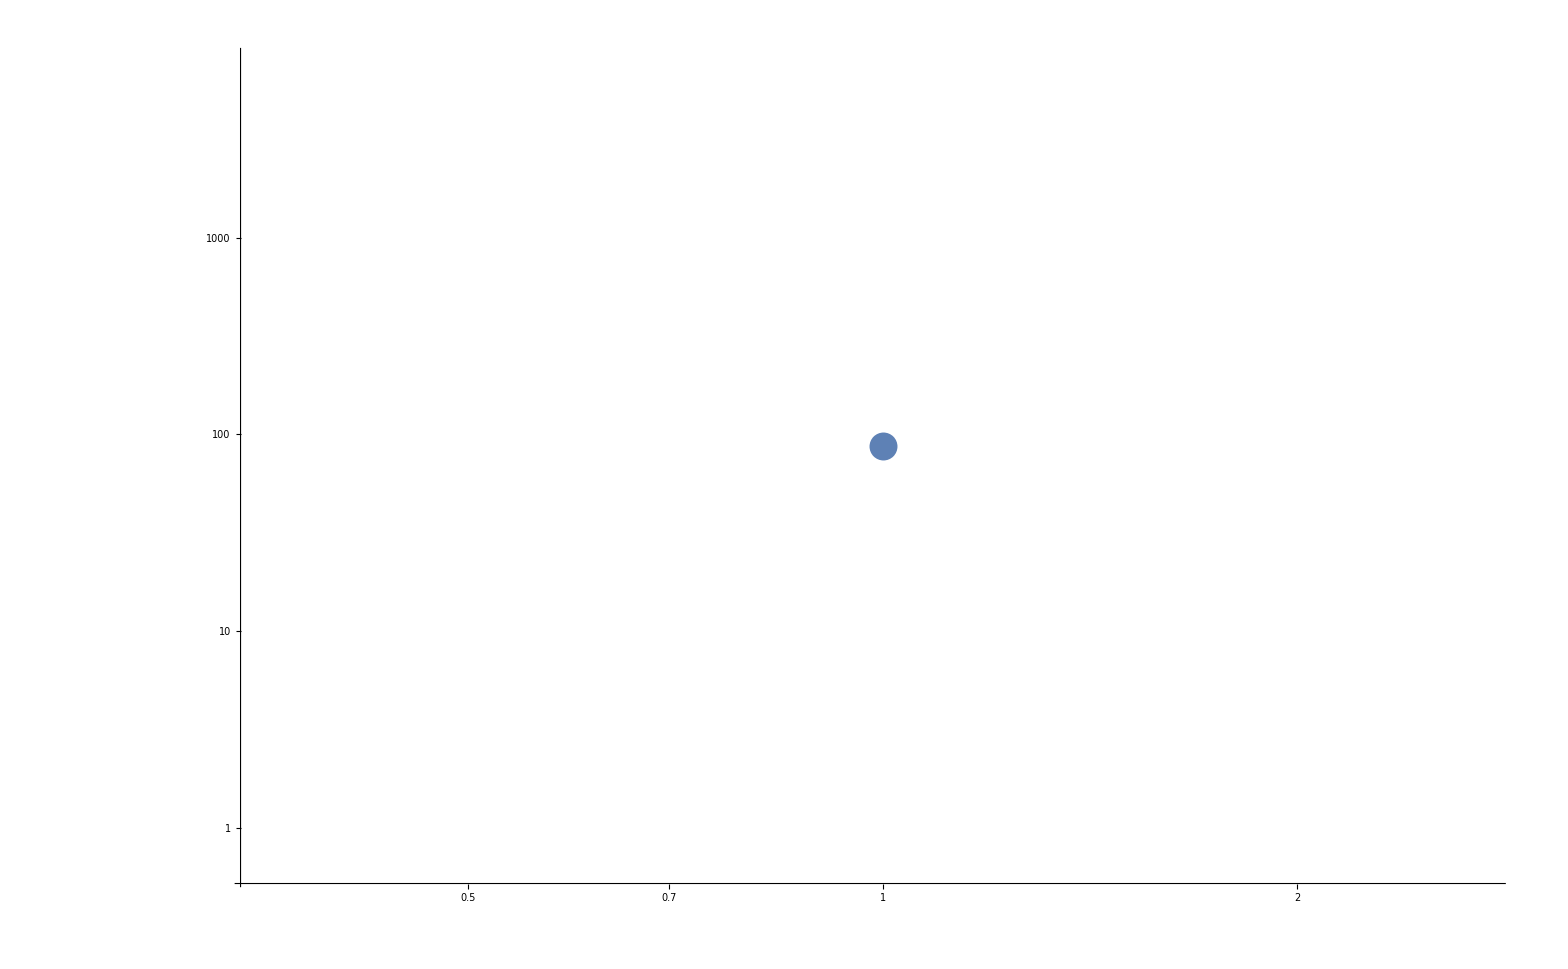

```mathematica
ListLogLogPlot[{chidata},PlotRange->All]
```

```mathematica
datanew=Import["array.txt", "CSV"]
```

{1}
 |  |  |  |

```mathematica
ArrayPlot[datanew, ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
chinewdata = Import["xi.txt", "CSV"]
```

{{0,1},{1,48},{2,14},{3,7},{4,0},{5,3},{6,4},{7,2},{8,0},{9,1},{10,1},{11,0},{12,1},{13,1},{14,1},{15,0},{16,0},{17,0},{18,1},{19,0},{20,0},{21,0},{22,0},{23,0},{24,1},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,1},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,1},{51,0},{52,0},{53,0},{54,0},{55,0},{56,0},{57,0},{58,0},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0},{67,0},{68,0},{69,0},{70,0},{71,0},{72,0},{73,0},{74,0},{75,0},{76,0},{77,0},{78,0},{79,0},{80,0},{81,0},{82,0},{83,0},{84,0},{85,0},{86,0},{87,0}}

```mathematica
dataacc=chinewdata;
dataacc[[All,2]]=88-Accumulate[(chinewdata[[All,2]])]
```

{87,39,25,18,18,15,11,9,9,8,7,7,6,5,4,4,4,4,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

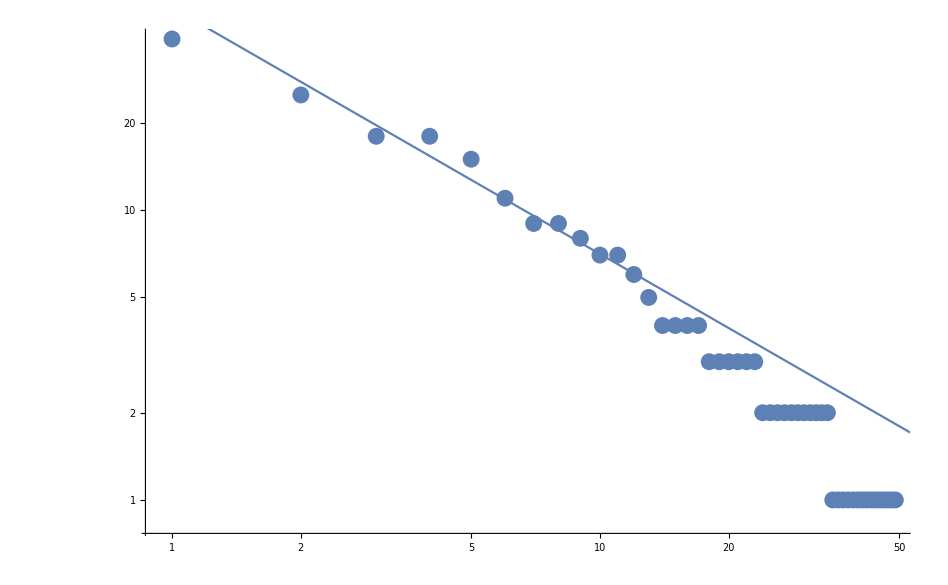

```mathematica
Show[ListLogLogPlot[{dataacc},PlotRange->All],LogLogPlot[50/(x^0.85),{x,0.5,10000}]]
```

```mathematica
f = Import["fplot.txt" , "CSV"];
```

```mathematica
fsort = f;
```

```mathematica
fsort[[1,All]]=SortBy[f,First];
```

```mathematica
facc=fsort;
facc[[1,All]]=Accumulate[(fsort[[1,All]])];
```

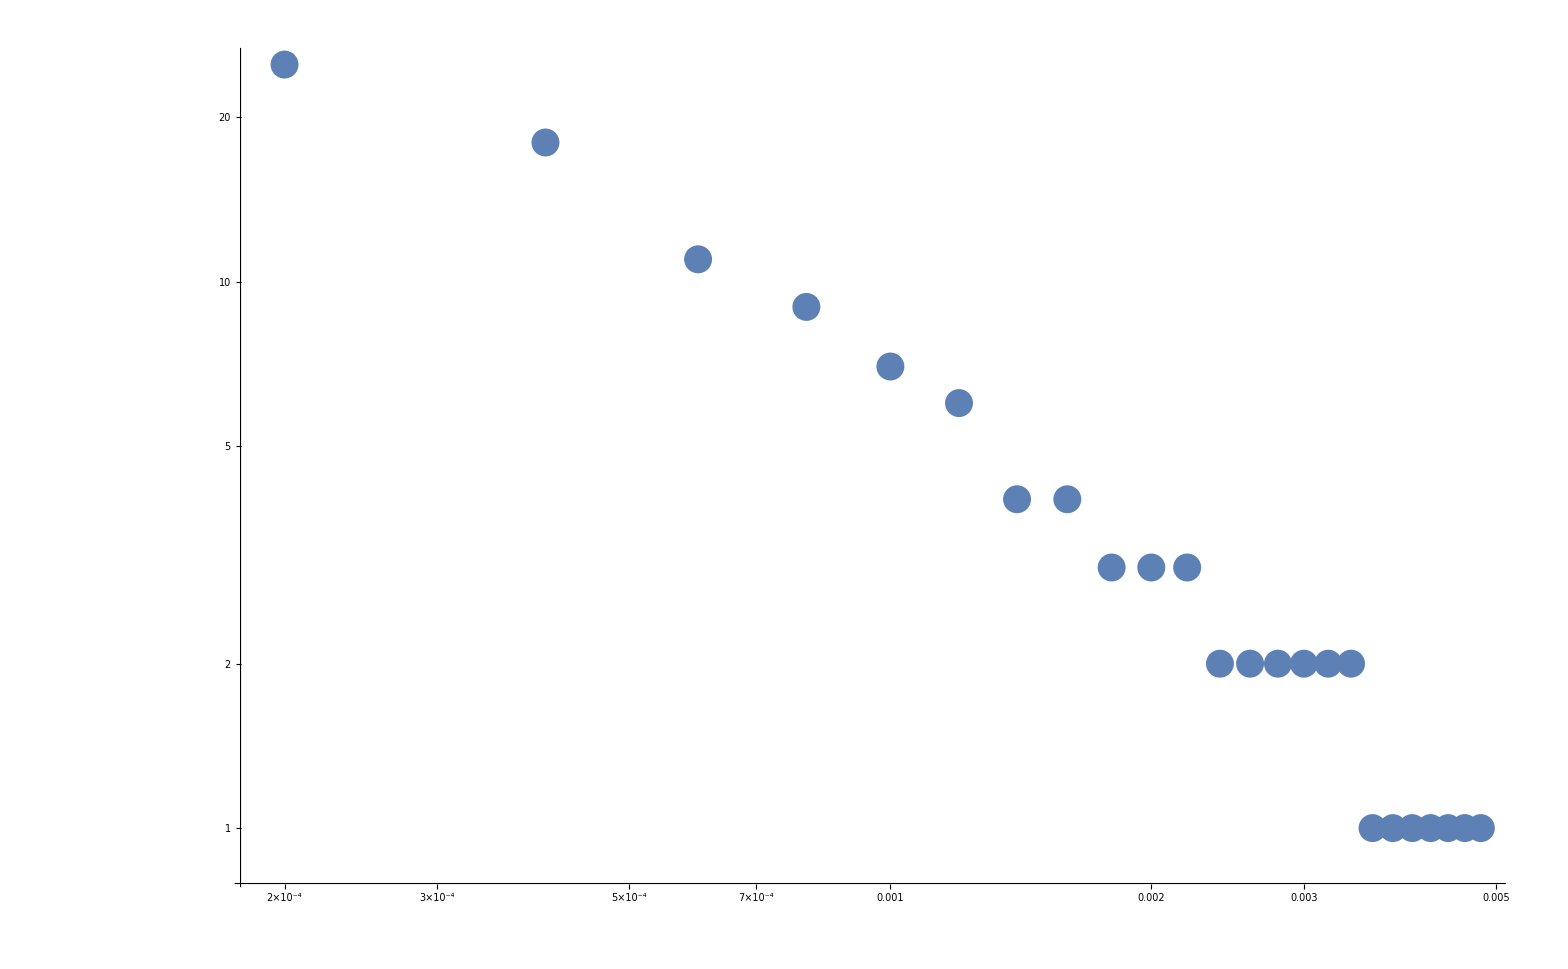

```mathematica
mutfreq=Import["mutfreq.txt","List"];
Table[{f,Length[Select[mutfreq,#>f&]]},{f,0,1,0.0002}];
ListLogLogPlot[%,PlotRange->All]
```

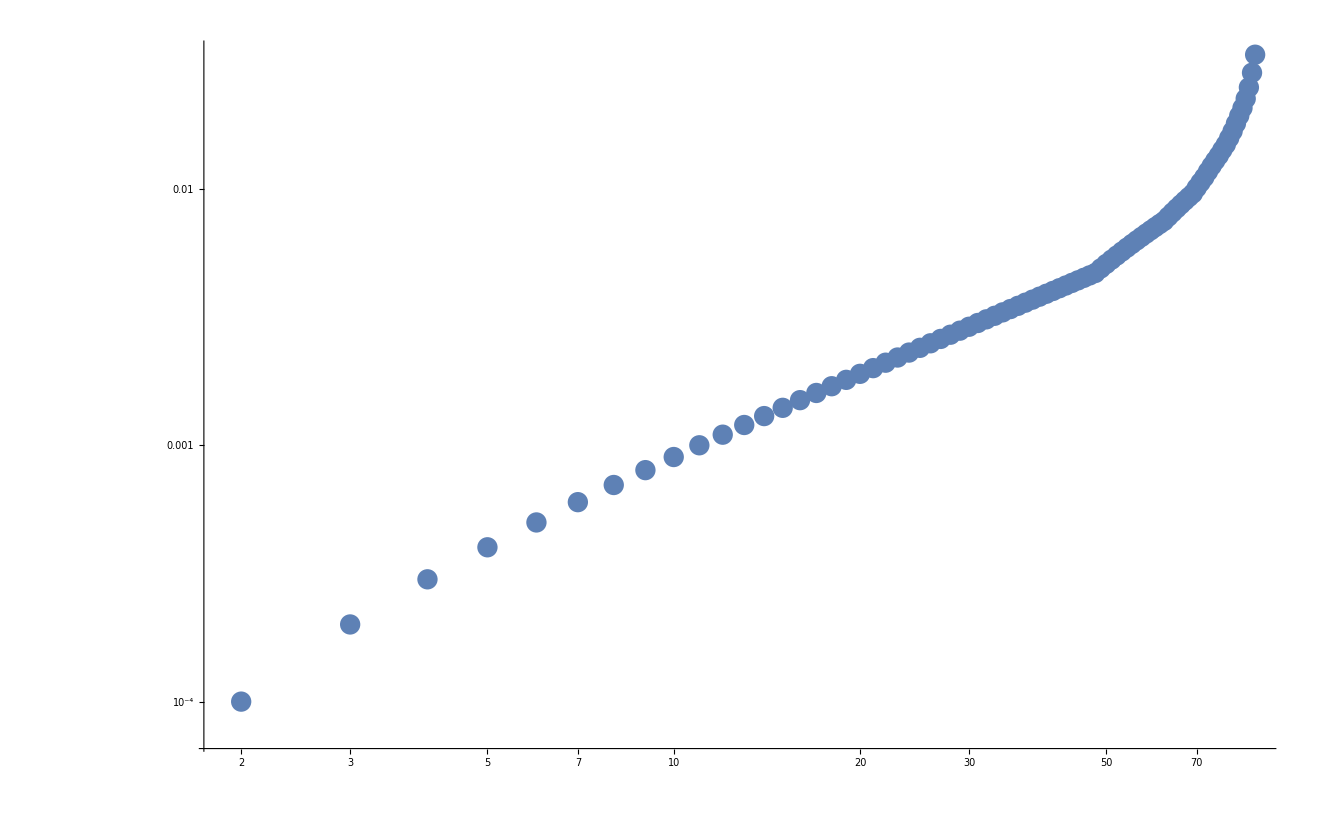

```mathematica
Mutsort  =Sort[mutfreq];
Mutacc = Accumulate[Mutsort];
ListLogLogPlot[Mutacc,PlotRange->All]
```